```mathematica
(* setting the parameters for the forward binomial tree *)
(* initial stock price *) S0=100;(* volatility *)σ=0.3; (* dividend yield *) δ=0; (* continuously compounded interest rate *)r=0.04; (* length of each period *) h=1; (* number of periods *) n=1;
```

```mathematica
T=n*h
```

1

```mathematica
(* up factor *) u = E^((r-δ)*h+σ*Sqrt[h])
```

1.40495

```mathematica
(* down factor *) d = E^((r-δ)*h-σ*Sqrt[h])
```

0.771052

```mathematica
(* risk-neutral probability *) pstar=1/(1+E^(σ*Sqrt[h]))
```

0.425557

```mathematica
(* strike price *) K=100
```

100

```mathematica
(* drawing Bernoulli trials *) LBern=RandomVariate[BernoulliDistribution[pstar],n]
```

{0}

```mathematica
(* cointosses from Bernoulli trials *) LCoinToss=-1+2*LBern
```

{-1}

```mathematica
(* prepending the origin *) LWalk=Prepend[Accumulate[LCoinToss],0]
```

{0,-1}

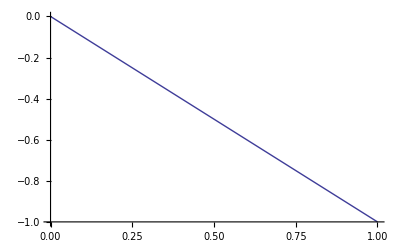

```mathematica
(* plotting the walk *) WalkToPlot[w_]:=Table[{i-1,w[[i]]}, {i,1,Length[w]}]; WalkToPlot[LWalk]; ListLinePlot[WalkToPlot[LWalk]]
```

```mathematica
(* height of the final position *) ht=LWalk[[n+1]]
```

-1

```mathematica
(* number of steps up *) upsteps= (ht+n)/2
```

0

```mathematica
(* number of steps down *) downsteps= n-upsteps
```

1

```mathematica
(* from cointosses to stock prices *) S1=S0* u^upsteps*d^downsteps
```

77.1052

```mathematica
(* from stock prices to the payoffs *) V1=Max[S1-K,0]
```

0

```mathematica
(* simulated price *) VSim= E^(-r*T)*V1
```

0.

```mathematica
(* analytic risk-neutral price *) VAn=E^(-r*T)*pstar*Max[S0*u-K,0]
```

16.5571

```mathematica
(* this is TERRIBLE -- we need to have MORE than one simulated final stock price !!! *)
```

```mathematica
(* number of simulations *) nsim=2
```

2

```mathematica
(* repeated Bernoulli trials *)LBernSims=Table[RandomVariate[BernoulliDistribution[pstar],n],{nsim}]
```

{{0},{0}}

```mathematica
(* cointosses from Bernoulli trials *) LCoinTossSims=-1+2*LBernSims
```

{{-1},{-1}}

```mathematica
(* prepending the origin *) LWalkSims=Table[ Prepend[Accumulate[LCoinTossSims[[i]]],0],{i,1,nsim}]
```

{{0,-1},{0,-1}}

```mathematica
(* formatted to plot *) PlotFormat=Table[WalkToPlot[LWalkSims[[i]]],{i,1,nsim}]
```

{{{0,0},{1,-1}},{{0,0},{1,-1}}}

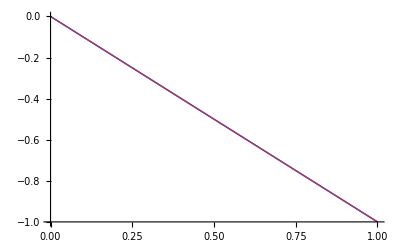

```mathematica
(* plotting *) ListLinePlot[PlotFormat]
```

```mathematica
(* height of the final position *) htSims=Table[LWalkSims[[i,n+1]], {i,1,nsim}]
```

{-1,-1}

```mathematica
(* number of steps up *) upstepsSims= (htSims+n)/2
```

{0,0}

```mathematica
(* number of steps down *) downstepsSims= n-upstepsSims
```

{1,1}

```mathematica
(* from cointosses to stock prices *) S1Sims=Table[S0*u^upstepsSims[[i]]*d^downstepsSims[[i]], {i,1,nsim}]
```

{77.1052,77.1052}

```mathematica
(* from stock prices to the payoffs *) V1Sims=Table[Max[S1Sims[[i]]-K,0],{i,1,nsim}]
```

{0,0}

```mathematica
(* simulated price *) VSim= E^(-r*T)*Total[V1Sims]/nsim
```

0.

```mathematica
(* we need a LOT of simulations !!!! *)
```

```mathematica
(* number of simulations *) nsim=200
```

200

```mathematica
(* repeated Bernoulli trials *)LBernSims=Table[RandomVariate[BernoulliDistribution[pstar],n],{nsim}];
```

```mathematica
(* cointosses from Bernoulli trials *) LCoinTossSims=-1+2*LBernSims;
```

```mathematica
(* prepending the origin *) LWalkSims=Table[ Prepend[Accumulate[LCoinTossSims[[i]]],0],{i,1,nsim}];
```

```mathematica
(* formatted to plot *) PlotFormat=Table[WalkToPlot[LWalkSims[[i]]],{i,1,nsim}];
```

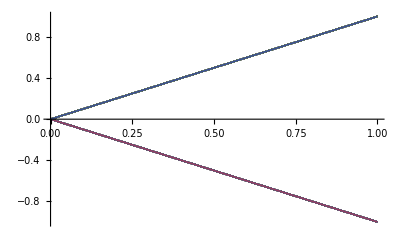

```mathematica
(* plotting *) ListLinePlot[PlotFormat]
```

```mathematica
(* height of the final position *) htSims=Table[LWalkSims[[i,n+1]], {i,1,nsim}];
```

```mathematica
(* number of steps up *) upstepsSims= (htSims+n)/2;
```

```mathematica
(* number of steps down *) downstepsSims= n-upstepsSims;
```

```mathematica
(* from cointosses to stock prices *) S1Sims=Table[S0*u^upstepsSims[[i]]*d^downstepsSims[[i]], {i,1,nsim}] ;
```

```mathematica
(* from stock prices to the payoffs *) V1Sims=Table[Max[S1Sims[[i]]-K,0],{i,1,nsim}];
```

```mathematica
(* simulated price *) VSim= E^(-r*T)*Total[V1Sims]/nsim
```

18.8699

```mathematica
(* MANY MANY more simulations ..... *)
```

```mathematica
(* number of simulations *) nsim=10000
```

10000

```mathematica
(* repeated Bernoulli trials *)LBernSims=Table[RandomVariate[BernoulliDistribution[pstar],n],{nsim}];
```

```mathematica
(* cointosses from Bernoulli trials *) LCoinTossSims=-1+2*LBernSims;
```

```mathematica
(* prepending the origin *) LWalkSims=Table[ Prepend[Accumulate[LCoinTossSims[[i]]],0],{i,1,nsim}];
```

```mathematica
(* formatted to plot *) PlotFormat=Table[WalkToPlot[LWalkSims[[i]]],{i,1,nsim}];
```

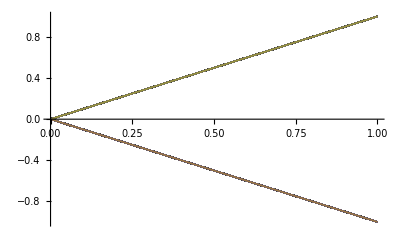

```mathematica
(* plotting *) ListLinePlot[PlotFormat]
```

```mathematica
(* height of the final position *) htSims=Table[LWalkSims[[i,n+1]], {i,1,nsim}];
```

```mathematica
(* number of steps up *) upstepsSims= (htSims+n)/2;
```

```mathematica
(* number of steps down *) downstepsSims= n-upstepsSims;
```

```mathematica
(* from cointosses to stock prices *) S1Sims=Table[S0*u^upstepsSims[[i]]*d^downstepsSims[[i]], {i,1,nsim}] ;
```

```mathematica
(* from stock prices to the payoffs *) V1Sims=Table[Max[S1Sims[[i]]-K,0],{i,1,nsim}];
```

```mathematica
(* simulated price *) VSim= E^(-r*T)*Total[V1Sims]/nsim
```

16.4265

```mathematica
(* how about more time periods? *) n=5
```

5

```mathematica
(* exercise date *) T=n*h
```

5

```mathematica
(* number of simulations *) nsim=1000
```

1000

```mathematica
(* repeated Bernoulli trials *)LBernSims=Table[RandomVariate[BernoulliDistribution[pstar],n],{nsim}];
```

```mathematica
(* cointosses from Bernoulli trials *) LCoinTossSims=-1+2*LBernSims;
```

```mathematica
(* prepending the origin *) LWalkSims=Table[ Prepend[Accumulate[LCoinTossSims[[i]]],0],{i,1,nsim}];
```

```mathematica
WalkToPlot[w_]:=Table[{i-1,w[[i]]}, {i,1,Length[w]}]; 
(* formatted to plot *) PlotFormat=Table[WalkToPlot[LWalkSims[[i]]],{i,1,nsim}];
```

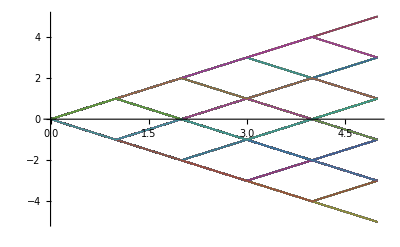

```mathematica
(* plotting *) ListLinePlot[PlotFormat]
```

```mathematica
(* height of the final position *) htSims=Table[LWalkSims[[i,n+1]], {i,1,nsim}];
```

```mathematica
(* number of steps up *) upstepsSims= (htSims+n)/2;
```

```mathematica
(* number of steps down *) downstepsSims= n-upstepsSims;
```

```mathematica
(* from cointosses to stock prices *) S1Sims=Table[S0*u^upstepsSims[[i]]*d^downstepsSims[[i]], {i,1,nsim}] ;
```

```mathematica
(* from stock prices to the payoffs *) V1Sims=Table[Max[S1Sims[[i]]-K,0],{i,1,nsim}];
```

```mathematica
(* simulated price *) VSim= E^(-r*T)*Total[V1Sims]/nsim
```

34.8634

```mathematica
(* analytic risk-neutral price *)VAn=E^(-r*T)*Expectation[Max[S0*u^x*d^(n-x)-K,0],x \[Distributed]BinomialDistribution[n,pstar]]
```

34.0766